```mathematica
Options[Singularity]={Angle->Pi/3,Even->True};
Singularity[pt1_List,pt2_List,width_,options___]:=Line[Module[{vecL,vecT,n,
length=Sqrt[(pt2-pt1).(pt2-pt1)],
relangle=Angle/.Flatten[{options},1]/.Options[Singularity],
even=Even/.Flatten[{options},1]/.Options[Singularity]},
n=Round[length/(2width Tan[relangle/2])]+If[even,0,1];
vecL=(pt2-pt1)/n;
vecT={-#1,#2}&@@Reverse[vecL];
vecT=vecT/Sqrt[vecT.vecT]width;
{pt1}~Join~{pt1+vecL}~Join~Table[pt1+(i+1/2) vecL-(-1)^i vecT,{i,1,n-2}]~Join~{pt2-vecL}~Join~{pt2}
]]
```

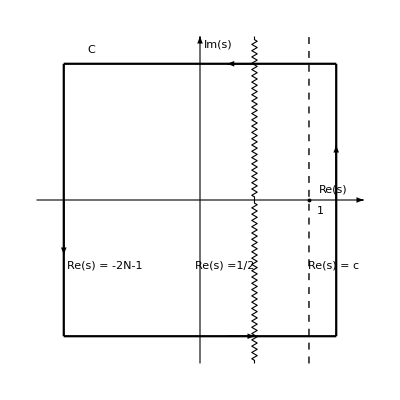

```mathematica
Show[Graphics[{
{Thickness[.002],Line[{{-3,0},{3,0}}]},
{Thickness[.002],Line[{{0,-3},{0,3}}]},
{Thickness[.004],Line[{{-2.5,-2.5},{-2.5,2.5}}]},
{Thickness[.004],Line[{{2.5,-2.5},{2.5,2.5}}]} ,
{Thickness[.004],Line[{{-2.5,-2.5},{2.5,-2.5}}]} ,
{PointSize[.007],Black,Point[{2,0}]},
{Dashed,Line[{{2,-3},{2,3}}]} ,
{Thickness[.002],Black,Singularity[{1,0},{1,3},.05]},
{Thickness[.002],Black,Singularity[{1,0},{1,-3},.05]},
{Thickness[.004],Line[{{-2.5,2.5},{2.5,2.5}}]} ,Text["Im(s)",{0.33,2.85}],Text["Re(s)",{2.45,0.2}],Text["1",{2.2,-0.2}],Text["Re(s) = c",{2.45,-1.2}],Text["C",{-2,2.75}],Text["Re(s) = -2N-1",{-1.75,-1.2}],Text["Re(s) =1/2",{0.45,-1.2}],{Arrowheads[.025],Arrow[{{0,2.95},{0,3}}]},
{Arrowheads[.025],Arrow[{{2.95,0},{3,0}}]},
{Arrowheads[.025],Arrow[{{2.5,0},{2.5,1}}]},
{Arrowheads[.025],Arrow[{{1,2.5},{0.5,2.5}}]},
{Arrowheads[.025],Arrow[{{-2.5,0},{-2.5,-1}}]},
{Arrowheads[.025],Arrow[{{0.5,-2.5},{1,-2.5}}]}
}],
PlotRange->{{-3.00,3.00},{-3.00,3.00}},AspectRatio->Automatic]
```

```mathematica
CohenMuSum[q_,n_,b_]:=∑_(a=1)^q If[Divisible[q,a]==True&&Divisible[n,a^b]==True,1,0]MoebiusMu[q/a] a^b
```

```mathematica
DivisorBeta[k_,n_,b_]:=∑_(d=1)^n If[Divisible[n,d^b]==True,1,0] d^(b*k)
```

```mathematica
MangoldtGeneral[b_,m_,n_]:=∑_(e=1)^n If[Divisible[n,e]==True,1,0]CohenMuSum[e,m,b]Log[n/e]
```

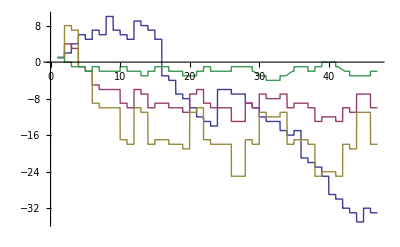

```mathematica
Plot[{∑_(q=1)^x CohenMuSum[q,24,1],∑_(q=1)^x CohenMuSum[q,24,2],∑_(q=1)^x CohenMuSum[q,24,3],∑_(q=1)^x CohenMuSum[q,24,4]},{x,1,47},Filling->None,AxesOrigin->{0,0}]
```

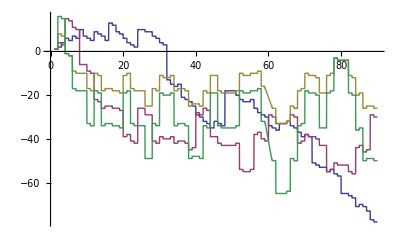

```mathematica
Plot[{∑_(q=1)^x CohenMuSum[q,48,1],∑_(q=1)^x CohenMuSum[q,48,2],∑_(q=1)^x CohenMuSum[q,48,3],∑_(q=1)^x CohenMuSum[q,48,4]},{x,1,90},Filling->None,AxesOrigin->{0,0}]
```

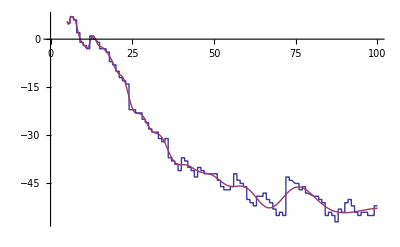

```mathematica
Plot[{∑_(q=1)^x CohenMuSum[q,12,1],-2DivisorBeta[1,12,1]+∑_(k=1)^5 (DivisorBeta[1-ZetaZero[k]/1,12,1]/Zeta'[ZetaZero[k]] x^ZetaZero[k]/ZetaZero[k]+DivisorBeta[1-(1-ZetaZero[k])/1,12,1]/Zeta'[1-ZetaZero[k]] x^(1-ZetaZero[k])/(1-ZetaZero[k]))+∑_(k=1)^50 DivisorBeta[1+2k/1,12,1]/Zeta'[-2k] x^(-2k)/(-2k)},{x,5,100},AxesOrigin->{0,0}]
```

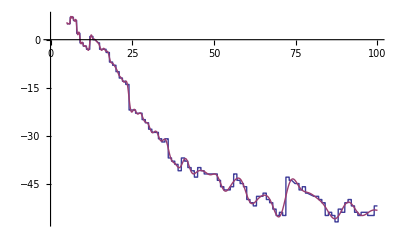

```mathematica
Plot[{∑_(q=1)^x CohenMuSum[q,12,1],-2DivisorBeta[1,12,1]+∑_(k=1)^25 (DivisorBeta[1-ZetaZero[k]/1,12,1]/Zeta'[ZetaZero[k]] x^ZetaZero[k]/ZetaZero[k]+DivisorBeta[1-(1-ZetaZero[k])/1,12,1]/Zeta'[1-ZetaZero[k]] x^(1-ZetaZero[k])/(1-ZetaZero[k]))+∑_(k=1)^50 DivisorBeta[1+2k/1,12,1]/Zeta'[-2k] x^(-2k)/(-2k)},{x,5,100},AxesOrigin->{0,0}]
```

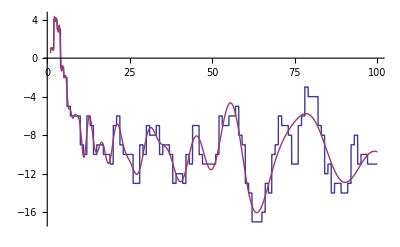

```mathematica
Plot[{∑_(q=1)^x CohenMuSum[q,24,2],-2DivisorBeta[1,24,2]+∑_(k=1)^5 (DivisorBeta[1-ZetaZero[k]/2,24,2]/Zeta'[ZetaZero[k]] x^ZetaZero[k]/ZetaZero[k]+DivisorBeta[1-(1-ZetaZero[k])/2,24,2]/Zeta'[1-ZetaZero[k]] x^(1-ZetaZero[k])/(1-ZetaZero[k]))+∑_(k=1)^50 DivisorBeta[1+2k/2,24,2]/Zeta'[-2k] x^(-2k)/(-2k)},{x,1,100}]
```

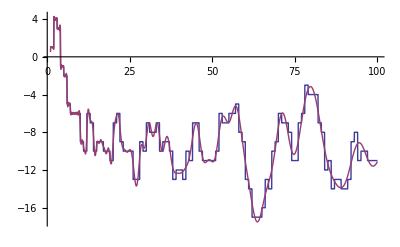

```mathematica
Plot[{∑_(q=1)^x CohenMuSum[q,24,2],-2DivisorBeta[1,24,2]+∑_(k=1)^25 (DivisorBeta[1-ZetaZero[k]/2,24,2]/Zeta'[ZetaZero[k]] x^ZetaZero[k]/ZetaZero[k]+DivisorBeta[1-(1-ZetaZero[k])/2,24,2]/Zeta'[1-ZetaZero[k]] x^(1-ZetaZero[k])/(1-ZetaZero[k]))+∑_(k=1)^50 DivisorBeta[1+2k/2,24,2]/Zeta'[-2k] x^(-2k)/(-2k)},{x,1,100}]
```

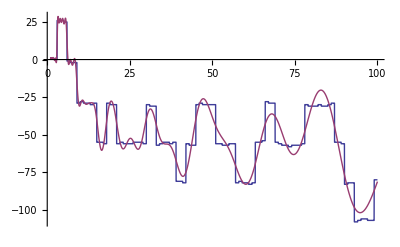

```mathematica
Plot[{∑_(q=1)^x CohenMuSum[q,810,3],-2DivisorBeta[1,810,3]+∑_(k=1)^5 (DivisorBeta[1-ZetaZero[k]/3,810,3]/Zeta'[ZetaZero[k]] x^ZetaZero[k]/ZetaZero[k]+DivisorBeta[1-(1-ZetaZero[k])/3,810,3]/Zeta'[1-ZetaZero[k]] x^(1-ZetaZero[k])/(1-ZetaZero[k]))+∑_(k=1)^50 DivisorBeta[1+2k/3,810,3]/Zeta'[-2k] x^(-2k)/(-2k)},{x,1,100}]
```

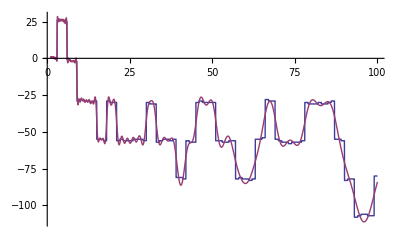

```mathematica
Plot[{∑_(q=1)^x CohenMuSum[q,810,3],-2DivisorBeta[1,810,3]+∑_(k=1)^25 (DivisorBeta[1-ZetaZero[k]/3,810,3]/Zeta'[ZetaZero[k]] x^ZetaZero[k]/ZetaZero[k]+DivisorBeta[1-(1-ZetaZero[k])/3,810,3]/Zeta'[1-ZetaZero[k]] x^(1-ZetaZero[k])/(1-ZetaZero[k]))+∑_(k=1)^50 DivisorBeta[1+2k/3,810,3]/Zeta'[-2k] x^(-2k)/(-2k)},{x,1,100}]
```

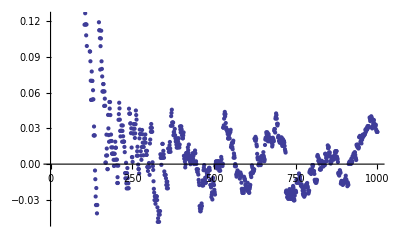

```mathematica
DiscretePlot[{∑_(q=1)^x CohenMuSum[q,24,1]/q},{x,1,1000},Filling->None,AxesOrigin->{0,0}]
```

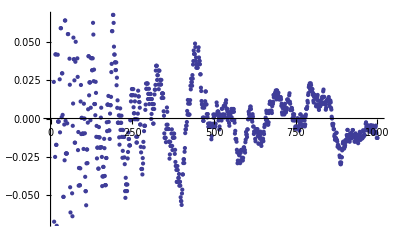

```mathematica
DiscretePlot[{∑_(q=1)^x CohenMuSum[q,24,2]/q},{x,1,1000},Filling->None,AxesOrigin->{0,0}]
```

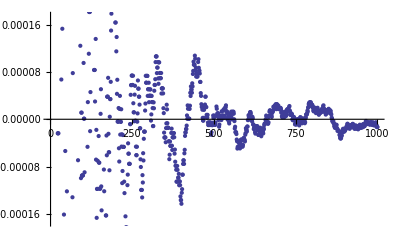

```mathematica
DiscretePlot[{∑_(q=1)^x CohenMuSum[q,24,2]/q^2-DivisorBeta[0,24,2]/Zeta[2]},{x,1,1000},Filling->None]
```

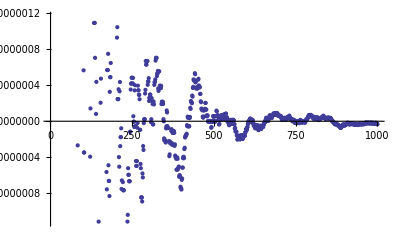

```mathematica
DiscretePlot[{∑_(q=1)^x CohenMuSum[q,24,3]/q^3-DivisorBeta[0,24,3]/Zeta[3]},{x,1,1000},Filling->None]
```

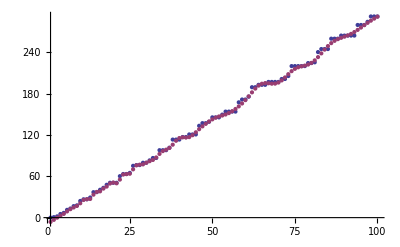

```mathematica
DiscretePlot[{∑_(q=1)^x MangoldtGeneral[2,12,q],DivisorBeta[1/2,12,2]x-DivisorBeta[1,12,2]Log[2π]-∑_(k=1)^10 (DivisorBeta[1-ZetaZero[k]/2,12,2] x^ZetaZero[k]/ZetaZero[k]+DivisorBeta[1-(1-ZetaZero[k])/2,12,2] x^(1-ZetaZero[k])/(1-ZetaZero[k]))},{x,1,100},Filling->None]
```

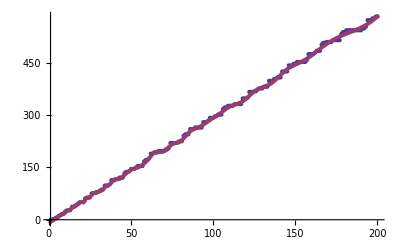

```mathematica
DiscretePlot[{∑_(q=1)^x MangoldtGeneral[2,12,q],DivisorBeta[1/2,12,2]x-DivisorBeta[1,12,2]Log[2π]-∑_(k=1)^10 (DivisorBeta[1-ZetaZero[k]/2,12,2] x^ZetaZero[k]/ZetaZero[k]+DivisorBeta[1-(1-ZetaZero[k])/2,12,2] x^(1-ZetaZero[k])/(1-ZetaZero[k]))},{x,1,200},Filling->None]
```

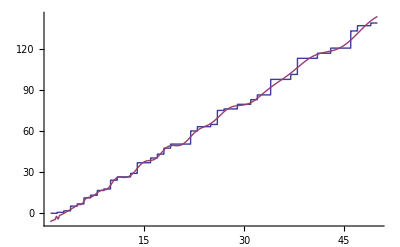

```mathematica
Plot[{∑_(q=1)^x MangoldtGeneral[2,12,q],DivisorBeta[1/2,12,2]x-DivisorBeta[1,12,2]Log[2π]-∑_(k=1)^5 (DivisorBeta[1-ZetaZero[k]/2,12,2] x^ZetaZero[k]/ZetaZero[k]+DivisorBeta[1-(1-ZetaZero[k])/2,12,2] x^(1-ZetaZero[k])/(1-ZetaZero[k]))},{x,1,50},Filling->None]
```

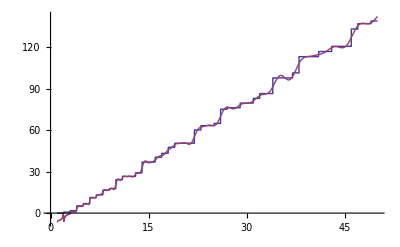

```mathematica
Plot[{∑_(q=1)^x MangoldtGeneral[2,12,q],DivisorBeta[1/2,12,2]x-DivisorBeta[1,12,2]Log[2π]-∑_(k=1)^25 (DivisorBeta[1-ZetaZero[k]/2,12,2] x^ZetaZero[k]/ZetaZero[k]+DivisorBeta[1-(1-ZetaZero[k])/2,12,2] x^(1-ZetaZero[k])/(1-ZetaZero[k]))},{x,1,50},Filling->None, AxesOrigin->{0,0}]
```

```mathematica
δ=2/10;β=1;n=12;X=100;Zeros=5;Tail1=20;DiscretePlot[{∑_(q=1)^x (1-q/x)^δ CohenMuSum[q,n,β],-2DivisorBeta[1,n,β]+∑_(k=1)^Zeros ((Gamma[1+δ]Gamma[ZetaZero[k]])/Gamma[1+δ+ZetaZero[k]] DivisorBeta[1-ZetaZero[k]/β,n,β]/Zeta'[ZetaZero[k]] x^ZetaZero[k]+(Gamma[1+δ]Gamma[1-ZetaZero[k]])/Gamma[1+δ+(1-ZetaZero[k])] DivisorBeta[1-(1-ZetaZero[k])/β,n,β]/Zeta'[1-ZetaZero[k]] x^(1-ZetaZero[k]))
+∑_(k=1)^Tail1 (Gamma[1+δ] π^(3/2+2k)Gamma[-1/2-k]DivisorBeta[1+(2k+1)/β,n,β])/((1+2k)!Gamma[1+k]Gamma[δ-2k]Zeta[2+2k])x^(-1-2k)
+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-2}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-4}]
+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-6}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-8}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-10}]},{x,1,X},AxesOrigin->{0,0},Filling->None]
```

-Graphics-

```mathematica
δ=2/10;β=1;n=12;X=100;Zeros=25;Tail1=20;Plot[{∑_(q=1)^x (1-q/x)^δ CohenMuSum[q,n,β],-2DivisorBeta[1,n,β]+∑_(k=1)^Zeros ((Gamma[1+δ]Gamma[ZetaZero[k]])/Gamma[1+δ+ZetaZero[k]] DivisorBeta[1-ZetaZero[k]/β,n,β]/Zeta'[ZetaZero[k]] x^ZetaZero[k]+(Gamma[1+δ]Gamma[1-ZetaZero[k]])/Gamma[1+δ+(1-ZetaZero[k])] DivisorBeta[1-(1-ZetaZero[k])/β,n,β]/Zeta'[1-ZetaZero[k]] x^(1-ZetaZero[k]))
+∑_(k=1)^Tail1 (Gamma[1+δ] π^(3/2+2k)Gamma[-1/2-k]DivisorBeta[1+(2k+1)/β,n,β])/((1+2k)!Gamma[1+k]Gamma[δ-2k]Zeta[2+2k])x^(-1-2k)
+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-2}]+
Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-4}]+
Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-6}]+
Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-8}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-10}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-12}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-14}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-16}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-18}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-20}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-22}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-24}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-26}]+
Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-28}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-30}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-32}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-34}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-36}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-38}]+Residue[(Gamma[1+δ]DivisorBeta[1-s/β,n,β])/Gamma[1+δ+s](π^(1/2-s)Gamma[s]Gamma[s/2])/(Gamma[(1-s)/2]Zeta[1-s])x^s,{s,-40}]},{x,1,X},AxesOrigin->{0,0},Filling->None]
```

$Aborted

```mathematica
MangoldtIvic[n_,k_]:=∑_(e=1)^n If[Divisible[n,e]==True,1,0]MoebiusMu[d](Log[e])^k
```

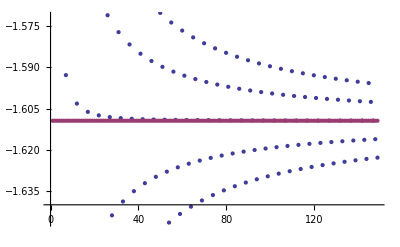

```mathematica
DiscretePlot[{∑_(n=1)^x CohenMuSum[5,n,1]/n,-MangoldtLambda[5]},{x,1,149},Filling->None]
```